# Basenspaß mit Maike

## The counting way

```mathematica
Simplify[RSolve[{m[k] == 3^(k-1)-m[k-1],m[0]==1},m[k],k] ](* solve the reccurrent relation for number of valid (i.e. on A ending) sequences of mutations*)
```

{{m[k]→1/4 (3 (-1)^k+3^k)}}

```mathematica
q [k] = Simplify[1/4 (4 (-1)^k+(-1)^(1+k)+3^k)/3^k] (* divide above expression by 3^k to get the ratio of valid sequences *)
```

1/4 3^-k (3 (-1)^k+3^k)

```mathematica
p[λ_,k_] = Exp[-λ]λ^k/Factorial[k] (* pdf of poisson *)
```

(ⅇ^-λ λ^k)/(k!)

```mathematica
Expand[Sum[p[x,k]q[k],{k,0,Infinity}]] (* there could have been 1 mutation, 2,3,.... this would be summing the p[x,k]. but we are interested in the relevant ones, so multiply with the ratio *)
```

1/4+3/4 ⅇ^(-4 x/3)

## The ODE way

```mathematica
(* The transition matrix: Since from A we CAN NOT GO TO A  (same for C G T) there is a -1 on the diagonal, be cause we DEFINITELY! go away from the old value. We switch with prob 1/3 to the other letters *)
```

```mathematica
M = {{-1,1/3,1/3,1/3},
{1/3,-1,1/3,1/3},
{1/3,1/3,-1,1/3},
{1/3,1/3,1/3,-1}
} ;
```

```mathematica
X[t_] = {m1[t],m2[t],m3[t],m4[t]}
```

{m1[t],m2[t],m3[t],m4[t]}

```mathematica
DSolve[{X'[t] == M.X[t],m1[0] == 1,m2[0] == 0,m3[0] == 0, m4[0] == 0},{m1,m2,m3,m4},t] (* Solve the ODE with IC pA = 1, all others = 0*)
```

{{m1→Function[{t},1/4 ⅇ^(-4 t/3) (3+ⅇ^(4 t/3))],m2→Function[{t},1/4 ⅇ^(-4 t/3) (-1+ⅇ^(4 t/3))],m3→Function[{t},1/4 ⅇ^(-4 t/3) (-1+ⅇ^(4 t/3))],m4→Function[{t},1/4 ⅇ^(-4 t/3) (-1+ⅇ^(4 t/3))]}}

```mathematica
(* first entry:*)
```

```mathematica
Expand[1/4 ⅇ^(-4 t/3) (3+ⅇ^(4 t/3))]
```

1/4+3/4 ⅇ^(-4 t/3)

Awesome, same thing!

## Now consider a sequence S \in {A,C,G,T}^N after time t

```mathematica
p[k_,r_,n_] = Binomial[n,k] r^k(1-r)^(n-k)
```

(1-r)^(-k+n) r^k Binomial[n,k]

```mathematica
pA[λ_] = 1/4+3/4Exp[-4/3λ] (* prob that letter stays the same *)
```

1/4+3/4 ⅇ^(-4 λ/3)

```mathematica
pC[λ_] = 1/4-1/4Exp[-4/3λ] (* prob that it moves from A to C,G or T*)
```

1/4-1/4 ⅇ^(-4 λ/3)

```mathematica
Manipulate[DiscretePlot[p[k,pA[r],n],{k,0,n},
PlotRange->Full],{r,0.0001,10},{n,Table[i,{i,100,1000}]}]
(* p[k,r,n] = prob that a sequence of length n matches with the original sequence after time t at k positions given a probability of a match of r where r = 1/4 + 3/4 exp(-4/3 lambda) Note: this is one mutated sequence to the original one, not two mutated sequences  *)
```

```mathematica
Manipulate[DiscretePlot[p[k,pA[r]*pA[r]+3*pC[r]*pC[r],n],{k,0,n},
PlotRange->Full],{r,0.0001,4},{n,Table[i,{i,100,1000}]}]
(* p[k,r,n] = prob that a sequence of length n matches with another  sequence after they both mutate originated from a base sequence after time t at k positions given a probability of a match of r where 
  r = prob that Seq1 does not mutate * prob that Seq2 does not mutate 
        + prob that Seq1 -> C * prob that Seq2 -> C + Seq1-> G*Seq2-> G ...
  *)
```

now plot both, prob base matches s1 and s2 matches s1

```mathematica
Manipulate[
DiscretePlot[
{
p[k,pA[r]*pA[r]+3*pC[r]*pC[r],n],
p[k,pA[r],n]
},{k,0,n},PlotRange->Full
],
{r,0.0001,5},
{n,Table[i,{i,100,1000}]}
]
```

```mathematica
Simplify[p[k,pA[r],n]] (*prob that sequence1 matches base (both of length n) at k positions given a mutation rate of r events pro time t *)
```

(3/4-3/4 ⅇ^(-4 r/3))^(-k+n) (1/4+3/4 ⅇ^(-4 r/3))^k Binomial[n,k]

```mathematica
Simplify[p[k,pA[r]*pA[r]+3*pC[r]*pC[r],n]] (*prob that sequence1 matches sequence2 (both of length n) at k positions given a mutation rate of r events pro time t *)
```

(3/4-3/4 ⅇ^(-8 r/3))^(-k+n) (1/4+3/4 ⅇ^(-8 r/3))^k Binomial[n,k]

```mathematica
Simplify[p[k,pA[2r],n]] (* note the 2r as an argument, i.e. twice the number of events / double the time *)
```

(3/4-3/4 ⅇ^(-8 r/3))^(-k+n) (1/4+3/4 ⅇ^(-8 r/3))^k Binomial[n,k]

(* Yay! This says: that to compare two sequences you just have to double the time (or the rate which would be equivalent) *)

# Next challenge: reverse: Given two sequences of same length, what is the prob that both mutated from the same origin

Assumptions: Sequence S1 and S2 of length n, matching at k positions. A mutation rate is fixed to be r in time t
Question: is t fixed to be 1?  Let’s say yes, i.e. what is the probability that we observe S1 and S2 and they both originated t time ago from the same base sequence given a mutation rate r. (afterwards we can vary t or r)

There are 4^n possible sequences.
Fix S1, for all sequences, we can compute the likelihood of each of the 4^n sequences (which works since the process is time reversible. let S be in {A,C,G,T}^N , then the prob that S1-> S = pA->A^number of times this happens * pA->C^.. * pA-> G^... * pA^T^... * pC^T ... * 
pStays^nstays *pChange^nchange 
Now we can compute the same prob for S-> S2
Then

for every sequence S , we know p(S1->S) and p(S2->S)
 Then the prob that both originated from the same sequence 
 is Sum over all Sequences p(S1->S)*p(S2->S)

## counting

if S of length N, how many S’ are there such that S and S’ are equal in n-k letters
if we want k missmatches

```mathematica
numberarrangments[n_,k_] = Binomial[n,k]*3^k
```

3^k Binomial[n,k]

```mathematica
(*Say you have 100 letters. you fix one sequence. How many of the 4^100 existing sequences have k missmatches? That's the plot below *)
```

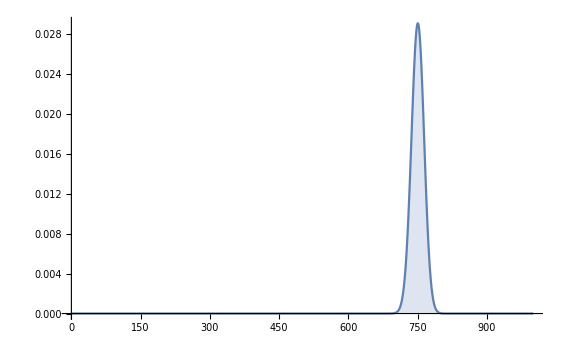

```mathematica
DiscretePlot[numberarrangments[1000,k]/4^1000,{k,0,1000},PlotRange->Full]
```

```mathematica
Sum[numberarrangments[100,k]/4^100,{k,0,100}]
```

1

```mathematica
probmutatekdiff[n_,k_,r_] = Simplify[numberarrangments[n,k] pA[r]^(n-k)pC[r]^k]
```

(3/4-3/4 ⅇ^(-4 r/3))^k (1/4+3/4 ⅇ^(-4 r/3))^(-k+n) Binomial[n,k]

```mathematica
Manipulate[DiscretePlot[probmutatekdiff[1090,k,r],{k,0,1090},PlotRange->Full],{r,0.0001,10}]
```

General::munfl: 0.0000999933^77 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000999933^78 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000999933^79 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.250029^1090 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.250029^1089 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.250029^1088 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.250029^1090 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.250029^1089 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.250029^1088 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Simplify[Sum[probmutatekdiff[n,k,r],{k,0,n}]]
```

1

```mathematica
f[n_,k_] =Simplify[3^k Binomial[n,k] - Sum[3^m Binomial[k,m]+3^(k-m)Binomial[n-m,k-m],{m,0,k}]]
```

-4^k-3^k Binomial[n,k] (-1+Hypergeometric2F1[1,-k,-n,1/3])

```mathematica
-4^k-3^k Binomial[n,k] (-1+Hypergeometric2F1[1,-k,-n,1/3])
```

-4^k-3^k Binomial[n,k] (-1+Hypergeometric2F1[1,-k,-n,1/3])

```mathematica
f[10,5]
```

-12950

```mathematica
ff[n_] =Simplify[Sum[ Sum[3^m Binomial[k,m]+3^(k-m)Binomial[n-m,k-m],{m,0,k}],{k,0,n}]]
```

1/3 (-1+4^(1+n)+3 DifferenceRoot[Function[{y,n},{(-6 n+6 n) y[n]+(-4+n-3 n) y[1+n]+(2+4 n-3 n) y[2+n]+(2+n) y[3+n]==0,y[0]==0,y[1]==1,y[2]==2+3 n}]][1+n])

```mathematica
p[n_,l_,r_] =  4^n pA[2r]^(n-l)pC[2r]^l
```

4^n (1/4-1/4 ⅇ^(-8 r/3))^l (1/4+3/4 ⅇ^(-8 r/3))^(-l+n)

```mathematica
Manipulate[Plot[4^n (1/4-1/4 ⅇ^(-8 r/3))^l (1/4+3/4 ⅇ^(-8 r/3))^(-l+n),{r,-0.9910755698198996,0.9910755698198996}],{l,-2.5,2.5},{n,0,100}]
```

```mathematica
Manipulate[DiscretePlot[pA[2r]^(10-l)pC[2r]^l,{l,0,10},PlotRange->Full],{r,0.0001,2}]
```

```mathematica
Sum[pA[2r]^(10-l)pC[2r]^l ,{l,0,10}]
```

(1/4-1/4 ⅇ^(-8 r/3))^10+(1/4-1/4 ⅇ^(-8 r/3))^9 (1/4+3/4 ⅇ^(-8 r/3))+(1/4-1/4 ⅇ^(-8 r/3))^8 (1/4+3/4 ⅇ^(-8 r/3))^2+(1/4-1/4 ⅇ^(-8 r/3))^7 (1/4+3/4 ⅇ^(-8 r/3))^3+(1/4-1/4 ⅇ^(-8 r/3))^6 (1/4+3/4 ⅇ^(-8 r/3))^4+(1/4-1/4 ⅇ^(-8 r/3))^5 (1/4+3/4 ⅇ^(-8 r/3))^5+(1/4-1/4 ⅇ^(-8 r/3))^4 (1/4+3/4 ⅇ^(-8 r/3))^6+(1/4-1/4 ⅇ^(-8 r/3))^3 (1/4+3/4 ⅇ^(-8 r/3))^7+(1/4-1/4 ⅇ^(-8 r/3))^2 (1/4+3/4 ⅇ^(-8 r/3))^8+(1/4-1/4 ⅇ^(-8 r/3)) (1/4+3/4 ⅇ^(-8 r/3))^9+(1/4+3/4 ⅇ^(-8 r/3))^10

```mathematica
Plot[%61,{r,0,1}]
```

-Graphics-

```mathematica
Simplify[1/4 ((1/4-1/4 ⅇ^(-8 r/3))^n-ⅇ^(8 r/3) (1/4-1/4 ⅇ^(-8 r/3))^n+3 (1/4+3/4 ⅇ^(-8 r/3))^n+ⅇ^(8 r/3) (1/4+3/4 ⅇ^(-8 r/3))^n)]
```

1/4 ((1/4-1/4 ⅇ^(-8 r/3))^n+3 (1/4+3/4 ⅇ^(-8 r/3))^n+ⅇ^(8 r/3) (-(1/4-1/4 ⅇ^(-8 r/3))^n+(1/4+3/4 ⅇ^(-8 r/3))^n))

```mathematica
Manipulate[Plot[1/4 ((1/4-1/4 ⅇ^(-8 r/3))^n+3 (1/4+3/4 ⅇ^(-8 r/3))^n+ⅇ^(8 r/3) (-(1/4-1/4 ⅇ^(-8 r/3))^n+(1/4+3/4 ⅇ^(-8 r/3))^n)),{r,6.496129592863984,7.216017305001947}],{n,-0.293285323844034,-0.26402645543204}]
```

## Number of sequences of length k that differ from S1 by n and from S2 by m where S1=AA...A and S2=CC...C

```mathematica
t[k_,n_,m_] = Factorial[k] / Factorial[k-n] /Factorial[k-m] / Factorial[n+m-k] 2^(n+m-k)
```

(2^(-k+m+n) k!)/((k-m)! (k-n)! (-k+m+n)!)

```mathematica
Manipulate[Table[t[k,n,m],{n,0,k},{m,0,k}]//MatrixForm,{k,1,10,1}]
```

```mathematica
Manipulate[MatrixPlot[Table[t[k,n,m]/4^k,{n,0,k},{m,0,k}]],{k,10,100,1}]
```

```mathematica
Manipulate[Sum[t[k,n,m],{n,0,k},{m,0,k}]-4^k,{k,1,10,1}]
```

t[k,n,m] = number of sequences of length k with difference n to S1 and difference m to S2 where the S1 = A...A and S2=C...C

if |s-s1| = n, then p(s->s1) = p^n*(1-p)^(k-n) where p is the prob of mutation = p_zz^k * p_z not z ^(n-k)


then given that S1 and S2 are completely different and of length K 
the prob that they have any common ancestor 
= sum_s  p(s->s1) * p(s->s2)
=

```mathematica
Simplify[Factorial[k]/Factorial[k-m]/Factorial[k-n]]
```

(k!)/((k-m)! (k-n)!)

```mathematica
x[r_,k_] = Sum[Factorial[k]/Factorial[k-m]/Factorial[k-n]*pC[r]^(n+m) * pA[r]^(2k-n-m),{n,0,k},{m,0,k}]
```

(ⅇ^((2 (3+ⅇ^(4 r/3)))/(-1+ⅇ^(4 r/3))) ((1/4+3/4 ⅇ^(-4 r/3)) (-1+ⅇ^(4 r/3)))^(2 k) (3+ⅇ^(4 r/3))^(-2 k) Gamma[1+k,(3+ⅇ^(4 r/3))/(-1+ⅇ^(4 r/3))]^2)/(k!)

```mathematica
Manipulate[DiscretePlot[x[r,k]/4^k,{k,0,10},PlotRange->Full],{r,0.000001,10}]
```

General::munfl: Exp[-3.×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.99998×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.99997×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

x[r,k] = the prob, that two sequences A...A and C...C share the same origin given rate r and length k (i.e. verrrrry unlikely)

```mathematica
N[x[100,1]]
```

0.25

does this make sense? assume rate is infinite and there are seq of length 1, i.e. A,C,G,T

plots

General::munfl: 9.44964×10^-293 1.77127×10^-17 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.57077×10^-294 1.8613×10^-17 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.21087×10^-295 1.95591×10^-17 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

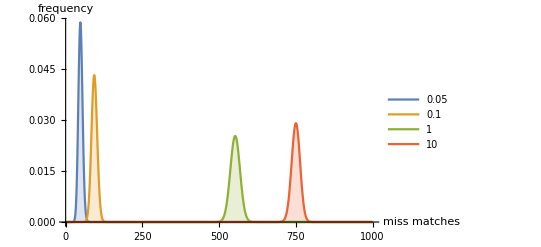

-Graphics-

```mathematica
DiscretePlot[{probmutatekdiff[1000,k,0.05],
probmutatekdiff[1000,k,0.1],
probmutatekdiff[1000,k,1],
probmutatekdiff[1000,k,10]
},{k,0,1000},PlotLegends->{0.05,0.1,1,10},PlotRange->Full, AxesLabel->{"miss matches","frequency"}]
```

## Distances

```mathematica
g[r_,n_,k_] =  pA[r]^(n-k)(1-pA[r])^k/3^k
```

3^-k (3/4-3/4 ⅇ^(-4 r/3))^k (1/4+3/4 ⅇ^(-4 r/3))^(-k+n)

```mathematica
Solve[D[g[r,n,k],r]==0,r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→-3/4 Log[-(4 k-3 n)/(3 n)]}}

```mathematica
dist[n_,k_] = -3/4 Log[-(4 k-3 n)/(3 n)];
```

```mathematica
Manipulate[DiscretePlot[Re[dist[n,k]],{k,0,n}],{n,1,100}]
```

```mathematica
Simplify[-3/4 Log[-(4 k-3 n)/(3 n)]]
```

-3/4 Log[1-(4 k)/(3 n)]

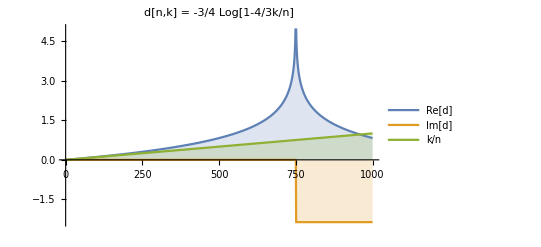

```mathematica
DiscretePlot[{Re[dist[1000,k]],Im[dist[1000,k]],k/1000},{k,0,1000},PlotRange->Full,PlotLegends->{"Re[d]","Im[d]","k/n"},
PlotLabel->"d[n,k] = -3/4 Log[1-4/3k/n]"]
```

Peak tends to infinity which makes sense. This is the number of differences one can expect for t\rightarrow \infty.

```mathematica
Im[Log[1-4/3]]
```

π

```mathematica
-3/4N[-Log[3]]
```

0.823959

```mathematica
Manipulate[Plot[pA[r]^(n-k)pC[r]^k,{r,0,5},PlotRange->Full],{k,0,n,1},{n,10,20,1}]
```

```mathematica
pA[r]^(n-k)pC[r]^k /. r-> Infinity
```

4^-n

```mathematica
Expand[g[r,n,k]]  /. r-> x*3/4
```

3^-k (3/4-(3 ⅇ^-x)/4)^k (1/4+(3 ⅇ^-x)/4)^(-k+n)

```mathematica
FullSimplify[(3/4-(3 ⅇ^-x)/4)^k (1/4+(3 ⅇ^-x)/4)^(-k+n)]
```

4^-n (3-3 ⅇ^-x)^k (1+3 ⅇ^-x)^(-k+n)

```mathematica
Simplify[(3-3Exp[-x])/(1+3Exp[-x])]
```

(3 (-1+ⅇ^x))/(3+ⅇ^x)

```mathematica
Solve[Simplify[Simplify[D[g[r,n,k],r]] /. k-> -x+3/4*n]==0,r]
```

{{r→3/4 (Log[3]-Log[4]+Log[n]-Log[x])}}

```mathematica
(4 (3/4-3/4 ⅇ^(-4 r/3))^(3 n/4) (1/4+3/4 ⅇ^(-4 r/3))^(n/4) n)/(-3+2 ⅇ^(4 r/3)+ⅇ^(8 r/3))
```

(4 (3/4-3/4 ⅇ^(-4 r/3))^(3 n/4) (1/4+3/4 ⅇ^(-4 r/3))^(n/4) n)/(-3+2 ⅇ^(4 r/3)+ⅇ^(8 r/3))

```mathematica
entropy[n_,k_,r_] = -k pA[r] Log[pA[r]]- (n-k) pC[r]Log[pC[r]]
```

-(1/4-1/4 ⅇ^(-4 r/3)) (-k+n) Log[1/4-1/4 ⅇ^(-4 r/3)]-(1/4+3/4 ⅇ^(-4 r/3)) k Log[1/4+3/4 ⅇ^(-4 r/3)]

```mathematica
Manipulate[MatrixPlot[Table[entropy[n,k,r],{n,1,100},{k,0,90}],PlotLegends->Automatic],{r,0.00001,0.2}]
```

```mathematica
entropy2[n_,k_,r_] = (-k *r* Log[r]- (n-k) (1-r)Log[(1-r)] )/n
```

(-(-k+n) (1-r) Log[1-r]-k r Log[r])/n

```mathematica
Manipulate[MatrixPlot[Table[entropy2[n,k,r],{n,1,100},{k,0,n}],PlotLegends->Automatic],{r,0.0,0.25}] (* k = x, n = y *)
```

```mathematica
Table[N[entropy2[n,k,r] /. r-> 0.9],{n,0,10},{k,0,n}] // MatrixForm
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

({Indeterminate}
{0.230259,0.0948245}
{0.230259,0.162541,0.0948245}
{0.230259,0.185114,0.139969,0.0948245}
{0.230259,0.1964,0.162541,0.128683,0.0948245}
{0.230259,0.203172,0.176085,0.148998,0.121911,0.0948245}
{0.230259,0.207686,0.185114,0.162541,0.139969,0.117397,0.0948245}
{0.230259,0.210911,0.191563,0.172215,0.152868,0.13352,0.114172,0.0948245}
{0.230259,0.213329,0.1964,0.179471,0.162541,0.145612,0.128683,0.111754,0.0948245}
{0.230259,0.21521,0.200162,0.185114,0.170066,0.155017,0.139969,0.124921,0.109873,0.0948245}
{0.230259,0.216715,0.203172,0.189628,0.176085,0.162541,0.148998,0.135455,0.121911,0.108368,0.0948245})

```mathematica
ent3[r_,n_,k_] = (3/4-3/4 ⅇ^(-4 r/3))^k (1/4+3/4 ⅇ^(-4 r/3))^(-k+n) Binomial[n,k]
```

(3/4-3/4 ⅇ^(-4 r/3))^k (1/4+3/4 ⅇ^(-4 r/3))^(-k+n) Binomial[n,k]

```mathematica
Manipulate[DiscretePlot[ent3[r,n,k],{k,0,n},PlotRange->Full],{r,0.00001,10},{n,10,100,1}]
```

```mathematica
Sum[ent3[r,n,k],{k,0,n}]
```

1

```mathematica
Manipulate[Plot[(pA[r]^(n-k)pC[r]^k) /(pA[r]^(1/4n)pC[r]^(3/4n)),{r,0,10},PlotRange->Full],{k,0,n,1},{n,100,200,1}]
```

General::munfl: 0.000068086^75 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000068086^105 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: 0.000068086^105 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: 0.000068086^105 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: 0.000068086^105 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: 0.000068086^105 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: 0.000068086^105 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: 0.000068086^105 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

```mathematica
pA[r]^(n-k)pC[r]^k /. r-> Infinity
```

4^-n

```mathematica
Simplify[D[pA[r]^(n-k)pC[r]^k ,r]]
```

(4 (1/4-1/4 ⅇ^(-4 r/3))^k (1/4+3/4 ⅇ^(-4 r/3))^(-k+n) (ⅇ^(4 r/3) (4 k-3 n)+3 n))/(3 (-3+2 ⅇ^(4 r/3)+ⅇ^(8 r/3)))

General::munfl: 0.0000340453^75 is too small to represent as a normalized machine number; precision may be lost.

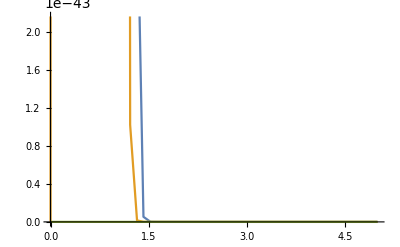

```mathematica
Plot[{pA[r]^(100-1)pC[r]^1,pA[r]^(100-10)pC[r]^10,pA[r]^(100-75)pC[r]^75},{r,0,5}]
```